Last modified on: Tuesday, July 10, 2018 at 23:13

Author Info

Sumner Magruder

Markus van Almsick

University of Hamburg

Poster Session Content

UpSetChart

Produce a chart for visualizing relationships between sets

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

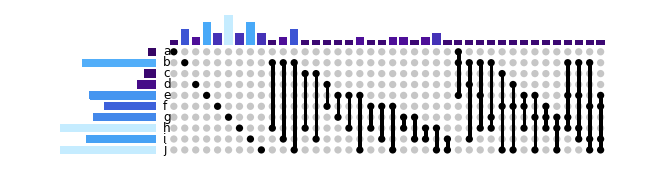

UpSetChart produces an interactive visualization allowing users to find what elements are unique to which intersections.

Add more customization options.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Visualizing sets

Often sets are visualized via a Venn Diagram:

-Graphics-
 six-set Venn Diagram from a 2012 Nature publication 
 
 However, it is hard to tell what part of this image corresponds to the intersections between which sets.

UpSetChart

UpSetChart is a way of visualizing set comparisons, similar to Venn Diagrams.  Unlike Venn Diagrams, UpSetChart provides direct insight into the cardinality of these comparisons as well as an indicator for what comparisons are being made.

sets = <|
"Red"→{"Strawberry","Apple"},
"Green"→{"Kiwi","Pear","Cucumber","Pickle"},
"Tasty"→{"Kiwi","Pear"},"Fruit"→{"Kiwi","Lemon","Banana","Strawberry","Pear","Apple","Carrot"},"Vegetable"→{"Cucumber","Pickle"}
|>;

Visualize all comparisons for these sets

Using UpSetChart makes it easy to visualize sets.

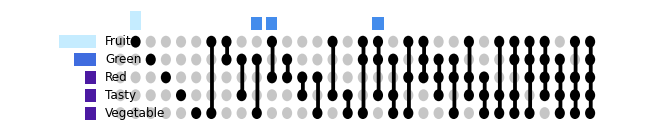
UpSetChart[sets,"DropEmpty"→False]
-Graphics-

Where the indicator grid corresponds to a part of a the Venn diagram.

Seeing what you care about

Since there are 2^n comparisons, like Venn-Diagrams, UpSetChart scales poorly; this can be ameliorated, however by dropping comparisons where there are no elements

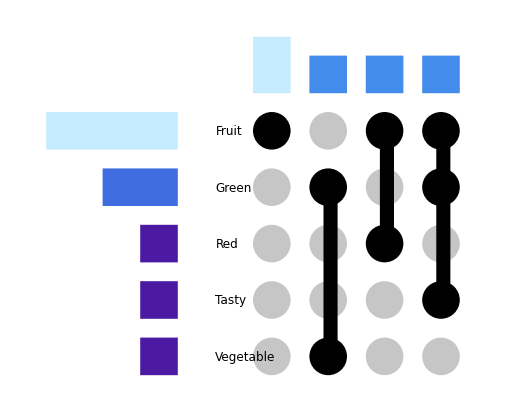
UpSetChart[sets,"DropEmpty"→True]
-Graphics-

Pushing the limits

For 20 sets there are 1,048,576 comparisons that would have to be visualized. Dropping empty sets, and sorting by cardinality allows for a clear overview of how these sets are related.

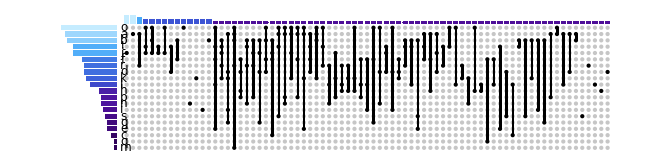
UpSetChart[RandomData[20],"DropEmpty"→True, "SetSortBy"→"Cardinality", "IntersectionSortBy"→ "Cardinality"]
-Graphics-

This is still a bit unwieldy, so by splitting this visualization up by the number of sets in each comparisons we can get an even clear insight to our data.

UpSetChart[RandomData[20],"DropEmpty"→True, "SetSortBy"→"Cardinality", "IntersectionSortBy"→ "Cardinality","TabbedByComparisonsDegreeQ"→True,"ImageSize"→{Automatic, 250}]
12345

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

A functional chart for set visualization.
Axes are available, but make the chart less robust due to hack required to implement them.

#### Code

Provide one of:

https://github.com/SumNeuron/WSS2018

#### Written Content / Lesson Plans

#### Conclusions in Detail

UpSetChart is a chart for visualizing comparisons between sets.
It comes with several options such as:

{“ColorGradient”, “DropEmpty” , “ComparisonSortBy”, “SetSortBy”,
  “Verbose”, “TabbedByComparisonsDegreeQ”,“ImageSize”}
  
  as well as a dynamic version DynamicUpSetChart with the same options

#### All Visualizations

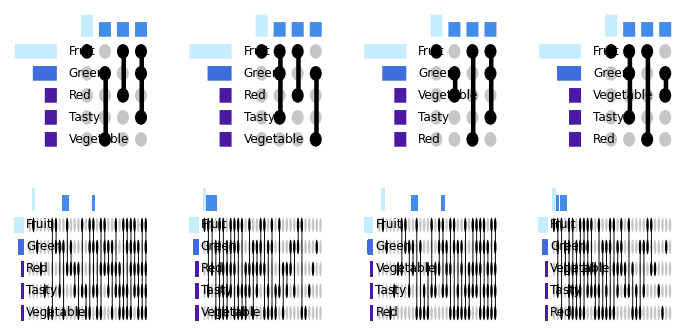

#### Data Sources Links/References

#### Future Directions

Add more options to try and match full coverage with options available with BarChart, e.g.

{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesStyle,Background,BaselinePosition,BaseStyle,ChartBaseStyle,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,ColorFunction,ColorFunctionScaling,ColorOutput,ContentSelectable,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,LabelingFunction,LabelingSize,LabelStyle,LegendAppearancePerformanceGoal,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotTheme, ScalingFunctions,TargetUnits,Ticks,
TicksStyle}

#### Background Info Links/References

Inspired by Caleydo

#### Keywords

Provide keywords as items

Intersection

Union

Visualization

Chart

#### Other information